# Invasion plots

## Plotting parameters

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
plotdir="Plots/";(*directory to save figures in*)
```

```mathematica
Pad={{60,10},{50,10}};  (*space around plot*)
letpos={.05,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.175,0.5};  (*relative location of y axis label position*)

inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xsize=5inches;
aspectratio=1/Sqrt[2];
```

## Life-cycle

### Haploid competition

Frequency of haploids from each sex

```mathematica
Subscript[freqHap, sex_]:=ParallelSum[Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}}]
```

Mean haploid fitness of gametes from each sex

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}}]/Subscript[freqHap, sex]
```

Frequencies of haploid genotypes from each sex following haploid competition, which occurs between gametes coming from the same sex

```mathematica
Subscript[fHapSel, x_,y_,z_,sex_]:=(Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex])/(Subscript[wbarHap, sex] Subscript[freqHap, sex])
```

### Random mating

Gametes from the two sexes pair at random

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP]=Subscript[fHapSel, xM,yM,zM,female] Subscript[fHapSel, xP,yP,zP,male]
```

### Sex determination

Determine the sex of newly formed diploids

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=Subscript[fDip, xM,yM,zM,xP,yP,zP] Subscript[psex, zM,xP,zP,sex]
```

where a diploid must become male or female

```mathematica
sumsex=Subscript[psex, zM_,xP_,zP_,male]->1-Subscript[psex, zM,xP,zP,female];
```

Rules for invasion of a dominant modifier into an XY system (relabeling males and females and females as males, as well as Y as W and X as Z makes the ancestral system ZW)

```mathematica
invXY={
Subscript[psex, M,Y,M,female]->0,(*always male if neo-SD allele wildtype and have Y*)
Subscript[psex, M,X,M,female]->1,(*always female neo-SD allele wildtype and have X from father*)
Subscript[psex, m,xP_,zP_,female]->k,(*female with probability k if mutation at the maternal neo-SD locus*)
Subscript[psex, zM_,xP_,m,female]->k (*female with probability k if mutation at the paternal neo-SD locus*)
};
```

### Diploid selection

Frequencies of diploids from each sex

```mathematica
Subscript[freqDip, sex_]:=ParallelSum[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

Mean diploid fitness in each sex

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]/Subscript[freqDip, sex]
```

Frequencies of diploid genotypes in each sex following diploid selection, which occurs separately in each sex (even if diploid selection is not direct competition between members of the same sex but instead viability selection, selection still effectively occurs ‘separately in each sex’ because the next generation is sired by 50% males and 50% females)

```mathematica
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=(Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex])/(Subscript[wbarDip, sex] Subscript[freqDip, sex])
```

### Meiosis

Gamete genotypes produced by diploids

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_]:=Subscript[fHapNext, x,y,z,sex]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

#### Segregation

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_]->1
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_]->1/2,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,sex_,x1_,A,z1_]->Subscript[α, sex] ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex]),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,sex_,x1_,A,z1_]->Subscript[α, sex] ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex]),
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x1_,A,z1_]->Subscript[α, sex](1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x2_,a,z1_]->(1-Subscript[α, sex])(1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x2_,A,z1_]->Subscript[α, sex] (recAXandAM+recAXnotAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(recAXandAM+recAXnotAM),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,A,z1_]->Subscript[α, sex](1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,a,z2_]->(1-Subscript[α, sex])(1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,A,z2_]->Subscript[α, sex] (recAXandAM+recAMnotAX),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(recAXandAM+recAMnotAX),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x2_,A,z1_]->Subscript[α, sex] (1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x1_,a,z1_]->(1-Subscript[α, male])(1-(recAXandAM+recAXnotAM)),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x1_,A,z1_]->Subscript[α, sex] (recAXandAM+recAXnotAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,sex_,x2_,a,z1_]->(1-Subscript[α, sex])(recAXandAM+recAXnotAM),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,A,z2_]->Subscript[α, sex] (1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,a,z1_]->(1-Subscript[α, sex])(1-(recAXandAM+recAMnotAX)),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,A,z1_]->Subscript[α, sex] (recAXandAM+recAMnotAX),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,sex_,x1_,a,z2_]->(1-Subscript[α, sex])(recAXandAM+recAMnotAX),
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_]->(1-(recAXnotAM+recAMnotAX))/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_]->(1-(recAXnotAM+recAMnotAX))/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_]->(recAXnotAM+recAMnotAX)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_]->(recAXnotAM+recAMnotAX)/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z1_]->Subscript[α, male](1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z2_]->(1-Subscript[α, male])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z1_]->Subscript[α, male] recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z2_]->Subscript[α, male] recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z1_]->(1-Subscript[α, male])recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z2_]->Subscript[α, male] recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z1_]->(1-Subscript[α, male])recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z2_]->Subscript[α, male] (1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z1_]->(1-Subscript[α, male])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z2_]->Subscript[α, male] recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z1_]->(1-Subscript[α, male])recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z1_]->Subscript[α, male] recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z1_]->Subscript[α, male] recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z2_]->(1-Subscript[α, male]) recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z1_]->Subscript[α, female](1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z2_]->(1-Subscript[α, female])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z1_]->Subscript[α, female] recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])recAXnotAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z2_]->Subscript[α, female] recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z1_]->(1-Subscript[α, female])recAMnotAX,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z2_]->Subscript[α, female] recAXandAM,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z2_]->Subscript[α, female] (1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z1_]->(1-Subscript[α, female])(1-recAMnotAX-recAXnotAM-recAXandAM),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z2_]->Subscript[α, female] recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z1_]->(1-Subscript[α, female])recAXnotAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z1_]->Subscript[α, female] recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])recAMnotAX,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z1_]->Subscript[α, female] recAXandAM,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z2_]->(1-Subscript[α, female]) recAXandAM
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_]->0;
```

#### Recombination probabilities for different arrangements of loci

Let the probability of recombination (an odd number of cross-overs) between loci A and X be r, the probability of recombination between A and M be R, and the probability of recombination between X and M be χ.

We can then write, in general,

```mathematica
recGen={
recAXnotAM->(r+χ-R)/2,
recAMnotAX->(R+χ-r)/2,
recAXandAM->(r+R-χ)/2
};
```

and for specific orders of loci we can substitute in the value of χ (alternatively one could do the same for R or r)

```mathematica
χAXM=χ->R(1-r)+r(1-R);
χXAM=χ->(r-R)/(1-2R);
χXMA=χ->(R-r)/(1-2r);
```

## Useful functions

We begin with no mutations at the modifer locus

```mathematica
subequil={
Subscript[fHap, X,A,M,female]->pXf,
Subscript[fHap, X,a,M,female]->1-pXf,
Subscript[fHap, X,A,M,male]->pXm *(1-freqYm),
Subscript[fHap, X,a,M,male]->(1-pXm)(1-freqYm),
Subscript[fHap, Y,A,M,male]->pYm freqYm,
Subscript[fHap, Y,a,M,male]->(1-pYm)freqYm,
Subscript[fHap, x_,y_,m,sex_]->0,
Subscript[fHap, Y,y_,M,female]->0
};
```

The recursions are

```mathematica
differenceEqs={
Subscript[fHapNext, X,A,M,female]-Subscript[fHap, X,A,M,female],
Subscript[fHapNext, X,A,M,male]-Subscript[fHap, X,A,M,male],
Subscript[fHapNext, Y,A,M,male]-Subscript[fHap, Y,A,M,male],
(Subscript[fHapNext, Y,A,M,male]+Subscript[fHapNext, Y,a,M,male])-(Subscript[fHap, Y,A,M,male]+Subscript[fHap, Y,a,M,male])
}/.subequil/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
```

Convert to shorter variables

```mathematica
varsub={Subscript[wDip, A,A,female]->FAA,Subscript[wDip, A,a,female]->FAa,Subscript[wDip, a,A,female]->FAa,Subscript[wDip, a,a,female]->Faa,Subscript[wDip, A,A,male]->MAA,Subscript[wDip, A,a,male]->MAa,Subscript[wDip, a,A,male]->MAa,Subscript[wDip, a,a,male]->Maa,Subscript[wHap, A,male]->MA,Subscript[wHap, a,male]->Ma,Subscript[wHap, A,female]->FA,Subscript[wHap, a,female]->Fa,Subscript[α, male]->MdA,Subscript[α, female]->FdA};
```

Haldane’s (1919) mapping function: probability of an odd number of crossovers between positions y and z (for y and z sufficiently far apart; Eq 3), where y and z are measured in centiMorgans

```mathematica
pcross[y_,z_]:=(1-Exp[-2*√((y-z)^2)/100])/2
```

Recombination probabilities (no interference)

```mathematica
setr[x_,a_,m_]:=
If[
x<m<a||a<m<x,
pcross[x,m](1-pcross[m,a])+(1-pcross[x,m])pcross[m,a],
pcross[x,a]
]
```

```mathematica
setR[x_,a_,m_]:=
If[
a<x<m||m<x<a,
pcross[a,x](1-pcross[x,m])+(1-pcross[a,x])pcross[x,m],
pcross[a,m]
]
```

```mathematica
setχ[x_,a_,m_]:=
If[
x<a<m||m<a<x,
pcross[x,a](1-pcross[a,m])+(1-pcross[x,a])pcross[a,m],
pcross[x,m]
]
```

## Invasion function for neo-W into XY

Change in haplotypes

```mathematica
(*differenceEqs/.varsub/.recGen//Simplify*)
```

Resident equilibria

```mathematica
Clear[equilXY]
equilXY[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:={pXf,pXm,pYm,freqYm}/.NSolve[{(-Fa (-1+pXf) (Faa Ma pXf (-1+pXm)+FAa MA (FdA-pXf) pXm)+FA pXf (-FAa Ma (FdA-pXf) (-1+pXm)-FAA MA (-1+pXf) pXm))/(Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm))),(FA pXf (MA MAA (1+2 (-1+freqYm) pXm) pYm+2 Ma MAa (-1+pYm) (pXm-freqYm pXm+MdA (-1+r)))+2 Fa (-1+pXf) ((-1+freqYm) Ma Maa pXm (-1+pYm)+MA MAa pYm (pXm-freqYm pXm-MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-2 Fa (-1+pXf) pYm (freqYm (Ma Maa (-1+pYm)-MA MAa pYm)-MA MAa MdA (-1+r))+FA pXf (MA MAA pYm+2 freqYm pYm (Ma MAa (-1+pYm)-MA MAA pYm)-2 Ma MAa MdA (-1+pYm) r))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-Fa (-1+pXf) ((-1+2 freqYm) Ma Maa (-1+pYm)+2 MA MAa pYm (-freqYm+MdA+r-2 MdA r))+FA pXf ((1-2 freqYm) MA MAA pYm+2 Ma MAa (-1+pYm) (-1+freqYm+MdA+r-2 MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm))))}=={0,0,0,0},{pXf,pXm,pYm,freqYm}]
```

Cut off trivial equilibria

```mathematica
cutoff=10^(-10);

Clear[sieveXY]
sieveXY[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equilXY[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,MdA,FdA,r,R,χ])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==4,write=Append[write,eq[[i]]]]];
Sort[write]]
```

Characteristic polynomial

```mathematica
(*charpolyk1/.meanF->femaleMeanFit/.varsub//Simplify*)
```

Invasion fitness

```mathematica
Clear[invasionplotXY]
invasionplotXY[tryFAA_,tryFAa_,tryFaa_,tryMAA_,tryMAa_,tryMaa_,tryMA_,tryMa_,tryFA_,tryFa_,tryMdA_,tryFdA_,tryr_,tryR_,tryχ_]:=
Block[{
temp=Flatten[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,tryr,tryR,tryχ]],
pXf=temp[[1]],
pXm=temp[[2]],
pYf=0,
pYm=temp[[3]],
freqYm=temp[[4]],
subs={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,MA->tryMA,Ma->tryMa,FA->tryFA,Fa->tryFa,MdA-> tryMdA,FdA-> tryFdA},
r=tryr,
R=tryR,
χ=tryχ
},
Max[λ/.NSolve[0==(λ^4 (2 Fa^2 (-1+freqYm) (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm) λ (Faa Ma (1-2 λ+2 pXf λ+(-1+freqYm) pXm (1+2 (-1+pXf) λ)-freqYm (pYm+2 (-1+pXf) λ))-2 FAa MA (freqYm pYm (-1+FdA+R-FdA R)+(-1+freqYm) pXm (1+FdA (-1+R)-R-λ+pXf λ)))+2 FA^2 (-1+freqYm) pXf (FAa Ma (-1+pXm)-FAA MA pXm) λ (2 FAa Ma (FdA (1+(-1+freqYm) pXm-freqYm pYm) (-1+R)+(-1+freqYm) pXf (-1+pXm) λ)-FAA MA (freqYm pYm+(-1+freqYm) pXm (-1+2 pXf λ)))-Fa FA (Faa Ma (2 FAa Ma (FdA (1+(-1+freqYm) pXm-freqYm pYm) (-1+R) (1-2 λ+2 pXf λ+(-1+freqYm) pXm (1+2 (-1+pXf) λ)-freqYm (pYm+2 (-1+pXf) λ))+(-1+freqYm) pXf (-1+pXm) λ (1-4 λ+4 pXf λ+(-1+freqYm) pXm (1+4 (-1+pXf) λ)-freqYm (pYm+4 (-1+pXf) λ)))+FAA MA (-(-1+freqYm)^2 pXm^2 (-1+2 λ+8 (-1+pXf) pXf λ^2)+freqYm pYm (-1-2 (-1+pXf) λ+freqYm (pYm+2 (-1+pXf) λ))+(-1+freqYm) pXm (1-2 λ-8 (-1+pXf) pXf λ^2+2 freqYm (pYm (-1+λ)+(-1+pXf) λ (-1+4 pXf λ)))))+2 FAa MA (FAA MA (freqYm^2 pYm^2 (-1+FdA+R-FdA R)-(-1+freqYm) freqYm pXm pYm (-2+λ+pXf λ+R (2-2 pXf λ)+2 FdA (-1+R) (-1+pXf λ))+(-1+freqYm)^2 pXm^2 (-1+R+λ+pXf λ-2 pXf R λ-4 pXf λ^2+4 pXf^2 λ^2+FdA (-1+R) (-1+2 pXf λ)))+2 FAa Ma (FdA^2 ((-1+freqYm)^2 pXm^2+freqYm pYm (-1+freqYm pYm)-(-1+freqYm) pXm (-1+2 freqYm pYm)) (-1+2 R)+(-1+freqYm) pXf (-1+pXm) λ (-freqYm pYm (-1+R)+(-1+freqYm) pXm (-1+R+2 λ-2 pXf λ))+FdA (-(-1+freqYm)^2 pXm^2 (-1+λ-2 pXf λ+R (2+(-1+2 pXf) λ))+freqYm pYm (-1-pXf λ+R (2+pXf λ)+freqYm (pYm-2 pYm R-pXf (-1+R) λ))+(-1+freqYm) pXm (1-λ+2 pXf λ+R (-2+λ-2 pXf λ)+freqYm (pXf (-1+R) λ+pYm (-2+λ-2 pXf λ+R (4-λ+2 pXf λ))))))))) (2 FA^2 (-1+freqYm) pXf (FAa Ma (-1+pXm)-FAA MA pXm) λ (FAa Ma (2 (-1+freqYm) pXf (-1+pXm) λ+FdA (1+(-1+freqYm) pXm-freqYm pYm) (-2+r+R+χ))+FAA MA (freqYm pYm (-1+χ)-(-1+freqYm) pXm (-1+2 pXf λ+χ)))+2 Fa^2 (-1+freqYm) (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm) λ (Faa Ma (1-2 λ+2 pXf λ+freqYm (-2 (-1+pXf) λ+pYm (-1+χ))+(-1+freqYm) pXm (1+2 (-1+pXf) λ-χ)-χ)+FAa MA ((-1+FdA) freqYm pYm (-2+r+R+χ)-(-1+freqYm) pXm (2-r-R-2 λ+2 pXf λ-χ+FdA (-2+r+R+χ))))-Fa FA (Faa Ma (FAa Ma (2 (-1+freqYm) pXf (-1+pXm) λ (1-4 λ+4 pXf λ+freqYm (-4 (-1+pXf) λ+pYm (-1+χ))+(-1+freqYm) pXm (1+4 (-1+pXf) λ-χ)-χ)-FdA (1+(-1+freqYm) pXm-freqYm pYm) (-2+r+R+χ) (-1+2 λ-2 pXf λ-(-1+freqYm) pXm (1+2 (-1+pXf) λ-χ)+χ+freqYm (pYm+2 (-1+pXf) λ-pYm χ)))+FAA MA (-(-1+freqYm)^2 pXm^2 (8 (-1+pXf) pXf λ^2-2 λ (-1+χ)-(-1+χ)^2)+freqYm pYm (1+2 (-1+pXf) λ+freqYm (-2 (-1+pXf) λ+pYm (-1+χ))-χ) (-1+χ)-(-1+freqYm) pXm (8 (-1+pXf) pXf λ^2-2 λ (-1+χ)-(-1+χ)^2+2 freqYm (pYm (-1+χ) (-1+λ+χ)-(-1+pXf) λ (-1+4 pXf λ+χ)))))+FAa MA (FAA MA ((-1+FdA) freqYm^2 pYm^2 (-1+χ) (-2+r+R+χ)-2 (-1+freqYm) freqYm pXm pYm (-2+R+λ+pXf λ-pXf R λ+3 χ-R χ-λ χ-χ^2-r (-1+pXf λ+χ)+FdA (-2+r+R+χ) (-1+pXf λ+χ))+(-1+freqYm)^2 pXm^2 (-2+R+2 λ+2 pXf λ-2 pXf R λ-8 pXf λ^2+8 pXf^2 λ^2+3 χ-R χ-2 λ χ-χ^2-r (-1+2 pXf λ+χ)+FdA (-2+r+R+χ) (-1+2 pXf λ+χ)))-2 FAa Ma (2 FdA^2 ((-1+freqYm)^2 pXm^2+freqYm pYm (-1+freqYm pYm)-(-1+freqYm) pXm (-1+2 freqYm pYm)) (-1+r+R) (-1+χ)+(-1+freqYm) pXf (-1+pXm) λ (freqYm pYm (-2+r+R+χ)-(-1+freqYm) pXm (-2+r+R+4 λ-4 pXf λ+χ))+FdA ((-1+freqYm)^2 pXm^2 (-2+2 λ-4 pXf λ+R (2-λ+2 pXf λ-2 χ)+r (2+(-1+2 pXf) λ-2 χ)+2 χ-λ χ+2 pXf λ χ)+freqYm pYm (2-2 R+2 pXf λ-pXf R λ-r (2+pXf λ-2 χ)-2 χ+2 R χ-pXf λ χ+freqYm (-2 pYm (-1+r+R) (-1+χ)+pXf λ (-2+r+R+χ)))-(-1+freqYm) pXm (2-2 R-2 λ+4 pXf λ+R λ-2 pXf R λ-2 χ+2 R χ+λ χ-2 pXf λ χ+r (-2+λ-2 pXf λ+2 χ)+freqYm (pXf λ (-2+r+R+χ)+pYm (-4+2 λ-4 pXf λ+R (4-λ+2 pXf λ-4 χ)+r (4+(-1+2 pXf) λ-4 χ)+4 χ-λ χ+2 pXf λ χ)))))))))/(16 (-1+freqYm)^4 (Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm)))^4)/.subs,λ]]-1
]
```

## Invasion function for neo-Y into ZW

Change in haplotypes

```mathematica
(*differenceEqs/.male->temp/.female->male/.temp->female/.varsub/.recGen/.pXf->pZm/.pXm->pZf/.pYm->pWf/.freqYm->freqWf//Simplify*)
```

Resident equilibria

```mathematica
Clear[equilZW]
equilZW[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:={pZm,pZf,pWf,freqWf}/.NSolve[{(Fa (-1+pZf) (MA MAa (MdA-pZm)+Ma Maa (-1+pZm)) pZm+FA pZf (-1+pZm) (Ma MAa (MdA-pZm)+MA MAA pZm))/(-Fa (-1+pZf) (Ma Maa (-1+pZm)-MA MAa pZm)+FA pZf (Ma MAa (-1+pZm)-MA MAA pZm)),(2 Fa (-1+pWf) (Faa (-1+freqWf) Ma pZf (-1+pZm)+FAa MA pZm (pZf-freqWf pZf+FdA (-1+r)))+FA pWf (FAA MA (1+2 (-1+freqWf) pZf) pZm-2 FAa Ma (-1+pZm) ((-1+freqWf) pZf+FdA r)))/(2 (Fa (-1+pWf) (Faa Ma (-1+pZm)-FAa MA pZm)+FA pWf (FAA MA pZm+FAa (Ma-Ma pZm)))),(FA pWf (FAA MA (1-2 freqWf pWf) pZm+2 FAa Ma (-1+pZm) (freqWf pWf+FdA (-1+r)))-2 Fa (-1+pWf) (Faa freqWf Ma pWf (-1+pZm)+FAa MA pZm (-freqWf pWf+FdA r)))/(2 (Fa (-1+pWf) (Faa Ma (-1+pZm)-FAa MA pZm)+FA pWf (FAA MA pZm+FAa (Ma-Ma pZm)))),(-Fa (-1+pWf) (Faa (-1+2 freqWf) Ma (-1+pZm)-2 FAa MA pZm (-1+FdA+freqWf+r-2 FdA r))+FA pWf (FAA (1-2 freqWf) MA pZm+2 FAa Ma (-1+pZm) (freqWf-r+FdA (-1+2 r))))/(2 (Fa (-1+pWf) (Faa Ma (-1+pZm)-FAa MA pZm)+FA pWf (FAA MA pZm+FAa (Ma-Ma pZm))))}=={0,0,0,0},{pZm,pZf,pWf,freqWf}]
```

Cut off trivial equilibria

```mathematica
cutoff=10^(-10);

Clear[sieveZW]
sieveZW[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equilZW[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,MdA,FdA,r,R,χ])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==4,write=Append[write,eq[[i]]]]];
Sort[write]]
```

Characteristic polynomial

```mathematica
(*charpolyk1/.male->temp/.female->male/.temp->female/.meanF->maleMeanFit/.varsub/.pXf->pZm/.pXm->pZf/.pYm->pWf/.freqYm->freqWf//Simplify*)
```

Invasion fitness

```mathematica
Clear[invasionplotZW]
invasionplotZW[tryFAA_,tryFAa_,tryFaa_,tryMAA_,tryMAa_,tryMaa_,tryMA_,tryMa_,tryFA_,tryFa_,tryMdA_,tryFdA_,tryr_,tryR_,tryχ_]:=
Block[{
temp=Flatten[sieveZW[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,tryr,tryR,tryχ]],
pZm=temp[[1]],
pZf=temp[[2]],
pWm=0,
pWf=temp[[3]],
freqWf=temp[[4]],
subs={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,MA->tryMA,Ma->tryMa,FA->tryFA,Fa->tryFa,MdA-> tryMdA,FdA-> tryFdA},
r=tryr,
R=tryR,
χ=tryχ
},
Max[λ/.NSolve[0==(λ^4 (-2 Fa^2 ((-1+freqWf) Ma Maa (-1+pZf) (-1+pZm) λ+MA MAa (MdA (-1+freqWf (pWf-pZf)+pZf) (-1+R)+(-1+freqWf+pZf-freqWf pZf) pZm λ)) (2 (-1+freqWf) MA MAa (-1+pZf) pZm λ+Ma Maa ((-1+pZf) (1+2 (-1+pZm) λ)+freqWf (pWf+2 (-1+pZm) λ+pZf (-1+2 λ-2 pZm λ))))+2 FA^2 (pZf (2 Ma MAa (-1+pZm) λ+MA (MAA-2 MAA pZm λ))+freqWf (-2 Ma MAa pZf (-1+pZm) λ+MA MAA (pWf-pZf+2 pZf pZm λ))) (pZf (-MA MAA pZm λ+Ma MAa (1+MdA (-1+R)-R-λ+pZm λ))+freqWf (MA MAA pZf pZm λ+Ma MAa ((-1+MdA) pWf (-1+R)+pZf (-1+MdA+R-MdA R+λ-pZm λ))))+Fa FA (-(-1+pZf) pZf (2 MA^2 MAa MAA pZm λ (-1+2 MdA (-1+R)+4 pZm λ)+2 Ma^2 Maa MAa (-1+pZm) λ (3+2 MdA (-1+R)-2 R-4 λ+4 pZm λ)+Ma MA (Maa MAA (1-2 λ-8 (-1+pZm) pZm λ^2)+4 MAa^2 (MdA^2 (-1+2 R)+pZm λ (-1+R+2 λ-2 pZm λ)+MdA (1-λ+2 pZm λ+R (-2+λ-2 pZm λ)))))+freqWf^2 (2 MA^2 MAa MAA pZm λ (pWf (1+pZf (-1+2 MdA (-1+R)))+pZf (-1+4 pZm λ+pZf (1+2 MdA-2 MdA R-4 pZm λ)))+2 Ma^2 Maa MAa (-1+pZm) λ (pWf (-2+3 pZf+2 MdA (-1+pZf) (-1+R)+2 R-2 pZf R)+pZf (2-2 R+2 MdA (-1+pZf+R-pZf R)-4 λ+4 pZm λ+pZf (-3+2 R+4 λ-4 pZm λ)))-Ma MA (Maa MAA (pWf^2+2 pWf (pZf (-1+λ)+(-1+pZm) λ)+pZf (2 (-1+pZm) λ (-1+4 pZm λ)+pZf (1-2 λ-8 (-1+pZm) pZm λ^2)))+4 MAa^2 (MdA^2 (pWf-pZf)^2 (-1+2 R)+(-1+pZf) pZm λ (pWf-pWf R+pZf (-1+R+2 λ-2 pZm λ))-MdA (pWf-pZf) (pWf (-1+2 R)+pZm (-1+R) λ+pZf (1-λ+2 pZm λ+R (-2+λ-2 pZm λ))))))+freqWf (2 Ma^2 Maa MAa (-1+pZm) λ (pWf (2-2 R+pZf (-3+2 R)+2 MdA (-1+pZf+R-pZf R))+pZf (-5+4 MdA (-1+pZf) (-1+R)+4 R+8 λ-8 pZm λ+pZf (6-4 R+8 (-1+pZm) λ)))+2 MA^2 MAa MAA pZm λ (pWf (-1+pZf+2 MdA pZf-2 MdA pZf R)+2 pZf (MdA (-1+2 pZf) (-1+R)+(-1+pZf) (-1+4 pZm λ)))+Ma MA (Maa MAA (pWf (1+2 pZf (-1+λ)+2 (-1+pZm) λ)+pZf (-1-2 (-2+pZm) λ+16 (-1+pZm) pZm λ^2-2 pZf (-1+2 λ+8 (-1+pZm) pZm λ^2)))-4 MAa^2 (MdA^2 (pWf-pZf) (-1+2 pZf) (-1+2 R)+(-1+pZf) pZm λ (pWf (-1+R)-2 pZf (-1+R+2 λ-2 pZm λ))+MdA (pWf (-1-pZm λ+R (2+pZm λ)+pZf (2-λ+2 pZm λ+R (-4+λ-2 pZm λ)))+pZf (1-λ+3 pZm λ+R (-2+λ-3 pZm λ)+2 pZf (-1+λ-2 pZm λ+R (2-λ+2 pZm λ))))))))) (Fa^2 (2 MA MAa (-1+freqWf+pZf-freqWf pZf) pZm λ+Ma Maa (freqWf (-2 (-1+pZm) λ+pZf (1+2 (-1+pZm) λ-χ)+pWf (-1+χ))-(-1+pZf) (1+2 (-1+pZm) λ-χ))) (2 (-1+freqWf) Ma Maa (-1+pZf) (-1+pZm) λ+MA MAa (2 (-1+freqWf+pZf-freqWf pZf) pZm λ+MdA (-1+freqWf (pWf-pZf)+pZf) (-2+r+R+χ)))-FA^2 (pZf (-2 Ma MAa (-1+pZm) λ+MA MAA (-1+2 pZm λ+χ))+freqWf (2 Ma MAa pZf (-1+pZm) λ+MA MAA (pWf (-1+χ)-pZf (-1+2 pZm λ+χ)))) (pZf (-2 MA MAA pZm λ+Ma MAa (2-r-R-2 λ+2 pZm λ-χ+MdA (-2+r+R+χ)))+freqWf (2 MA MAA pZf pZm λ+Ma MAa ((-1+MdA) pWf (-2+r+R+χ)+pZf (-2+r+R+2 λ-2 pZm λ+χ-MdA (-2+r+R+χ)))))+Fa FA (-(-1+pZf) pZf (2 Ma^2 Maa MAa (-1+pZm) λ (3-r-R-4 λ+4 pZm λ-2 χ+MdA (-2+r+R+χ))+2 MA^2 MAa MAA pZm λ (-1+4 pZm λ+χ+MdA (-2+r+R+χ))+Ma MA (Maa MAA (-8 (-1+pZm) pZm λ^2+2 λ (-1+χ)+(-1+χ)^2)+2 MAa^2 (-2 MdA^2 (-1+r+R) (-1+χ)+pZm λ (-2+r+R+4 λ-4 pZm λ+χ)+MdA (2-2 λ+4 pZm λ-2 χ+λ χ-2 pZm λ χ+r (-2+λ-2 pZm λ+2 χ)+R (-2+λ-2 pZm λ+2 χ)))))+freqWf^2 (2 Ma^2 Maa MAa (-1+pZm) λ (pWf (-2+r+R+χ+MdA (-1+pZf) (-2+r+R+χ)-pZf (-3+r+R+2 χ))-pZf (-2+r+R+4 λ-4 pZm λ+χ+MdA (-1+pZf) (-2+r+R+χ)-pZf (-3+r+R+4 λ-4 pZm λ+2 χ)))+2 MA^2 MAa MAA pZm λ (pWf (1-χ+pZf (-1+χ+MdA (-2+r+R+χ)))-pZf (1-4 pZm λ-χ+pZf (-1+4 pZm λ+χ+MdA (-2+r+R+χ))))-Ma MA (Maa MAA (pWf^2 (-1+χ)^2-2 pWf (-1+χ) ((-1+pZm) λ+pZf (-1+λ+χ))+pZf (pZf (-8 (-1+pZm) pZm λ^2+2 λ (-1+χ)+(-1+χ)^2)+2 (-1+pZm) λ (-1+4 pZm λ+χ)))-2 MAa^2 (2 MdA^2 (pWf-pZf)^2 (-1+r+R) (-1+χ)+(-1+pZf) pZm λ (pWf (-2+r+R+χ)-pZf (-2+r+R+4 λ-4 pZm λ+χ))-MdA (pWf-pZf) (2 pWf (-1+r+R) (-1+χ)-pZm λ (-2+r+R+χ)+pZf (-2+2 λ-4 pZm λ+R (2-λ+2 pZm λ-2 χ)+r (2+(-1+2 pZm) λ-2 χ)+2 χ-λ χ+2 pZm λ χ)))))-freqWf (2 Ma^2 Maa MAa (-1+pZm) λ (pWf (-2+r+R+χ+MdA (-1+pZf) (-2+r+R+χ)-pZf (-3+r+R+2 χ))+pZf (5-2 r-2 R-8 λ+8 pZm λ-3 χ-2 MdA (-1+pZf) (-2+r+R+χ)+2 pZf (-3+r+R+4 λ-4 pZm λ+2 χ)))+2 MA^2 MAa MAA pZm λ (pZf (-MdA (-1+2 pZf) (-2+r+R+χ)-2 (-1+pZf) (-1+4 pZm λ+χ))+pWf (1-χ+pZf (-1+χ+MdA (-2+r+R+χ))))+Ma MA (Maa MAA (pZf (-16 (-1+pZm) pZm λ^2+2 pZf (8 (-1+pZm) pZm λ^2-2 λ (-1+χ)-(-1+χ)^2)-2 (-2+pZm) λ (-1+χ)+(-1+χ)^2)+pWf (-1+χ) (1+2 (-1+pZm) λ-χ+2 pZf (-1+λ+χ)))-2 MAa^2 (2 MdA^2 (pWf-pZf) (-1+2 pZf) (-1+r+R) (-1+χ)-(-1+pZf) pZm λ (pWf (-2+r+R+χ)-2 pZf (-2+r+R+4 λ-4 pZm λ+χ))+MdA (pWf (2-2 r-2 R+2 pZm λ-pZm r λ-pZm R λ-2 χ+2 r χ+2 R χ-pZm λ χ+pZf (-4+2 λ-4 pZm λ+R (4-λ+2 pZm λ-4 χ)+r (4+(-1+2 pZm) λ-4 χ)+4 χ-λ χ+2 pZm λ χ))-pZf (2-2 R-2 λ+6 pZm λ+R λ-3 pZm R λ-2 χ+2 R χ+λ χ-3 pZm λ χ+r (-2+λ-3 pZm λ+2 χ)+pZf (-4+4 λ-8 pZm λ+R (4-2 λ+4 pZm λ-4 χ)+r (4+(-2+4 pZm) λ-4 χ)+4 χ-2 λ χ+4 pZm λ χ)))))))))/(16 (-1+freqWf)^4 (Fa (Ma Maa (-1+pWf)-MA MAa pWf) (-1+pZm)+FA (MA MAA pWf+Ma (MAa-MAa pWf)) pZm)^4)/.subs,λ]]-1
]
```

## Position plots

### Plotting parameters

```mathematica
x=-25;
m=25;
Clear[a]

xplotmin=-50;
xplotmax=50;
xplotinterval=25;
yplotmin=-0.04;
yplotmax=0.05;
yplotinterval=0.02;
npoints=20;
```

### A. No haploid selection, sex antagonism - neo-SD only invades if more closely linked to A: equivalent to van Doorn and Kirkpatrick

#### Parameters

```mathematica
trysAf=0.1;
tryhAf=0.3;
tryhAm=0.3;
trysAm=0.1;
tryt=0;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1;
tryMAa=1+tryhAm trysAm;
tryMaa=1+trysAm;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;
```

#### Plot

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

Part::partw: Part 4 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

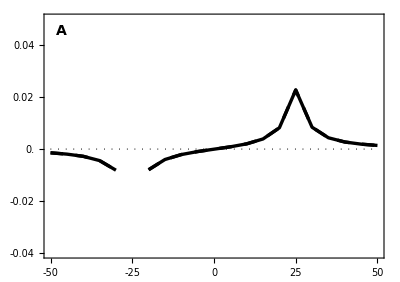

```mathematica
positionplotA=
Show[

(*neo-W into XY*)
ListPlot[Table[{a,invasionplotXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a,m],setR[x,a,m],setχ[x,a,m]]},{a,xplotmin,xplotmax,(xplotmax-xplotmin)/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

(*neo-Y into ZW*)
ListPlot[Table[{a,invasionplotZW[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a,m],setR[x,a,m],setχ[x,a,m]]},{a,xplotmin,xplotmax,(xplotmax-xplotmin)/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd],Dashing[Medium]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

Plot[0,{x,xplotmin,xplotmax},PlotStyle->{Black, Dotted}],

PlotRange->{{xplotmin,xplotmax},{yplotmin,yplotmax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,yplotinterval}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{(*"Chromosomal position of selected locus (cM)"*)"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Rotate[Text[Style["Invasion fitness",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False

]

Export[plotdir<>"PositionPlotA.pdf",%];
```

### B. Drive with no sex differences in selection and no sex ant - neo-SD always invades

#### Parameters

```mathematica
trysAf=0.1;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.1;
tryt=0;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.45;
tryFdA=0.5;
```

#### Plot

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

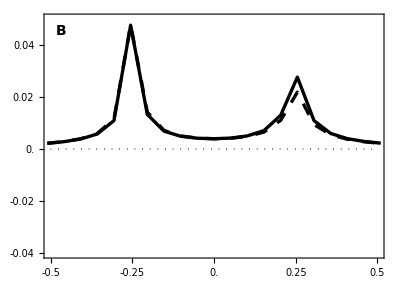

```mathematica
positionplotB=
Show[

(*neo-W into XY*)
ListPlot[Table[{a,invasionplotXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a,m],setR[x,a,m],setχ[x,a,m]]},{a,xplotmin-0.01,xplotmax+0.01,((xplotmax+0.01)-(xplotmin-0.01))/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

(*neo-Y into ZW*)
ListPlot[Table[{a,invasionplotZW[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a,m],setR[x,a,m],setχ[x,a,m]]},{a,xplotmin-0.01,xplotmax+0.01,((xplotmax+0.01)-(xplotmin-0.01))/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd],Dashing[Medium]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

Plot[0,{x,xplotmin,xplotmax},PlotStyle->{Black, Dotted}],

PlotRange->{{xplotmin,xplotmax},{yplotmin,yplotmax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,yplotinterval}]},
FrameTicksStyle->{{Directive[FontColor->White],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{(*"Chromosomal position of selected locus (cM)"*)"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
(*Rotate[Text[Style["Invasion fitness",14],Scaled@ylabpos],90 Degree]*)
},
PlotRangeClipping->False

]

Export[plotdir<>"PositionPlotB.pdf",%];
```

### C. Hap competition with sex differences in selection but not sex ant - but in other direction so neo-SD only invades if closely linked to A

#### Parameters

```mathematica
trysAf=0.15;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.05;
tryt=-0.1;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;
```

#### Plot

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

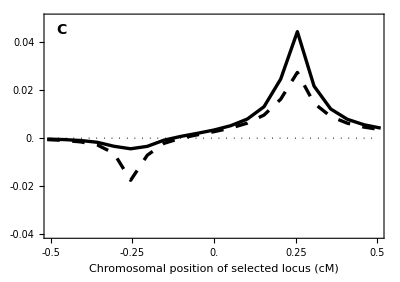

```mathematica
positionplotC=
Show[

(*neo-W into XY*)
ListPlot[Table[{a,invasionplotXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a,m],setR[x,a,m],setχ[x,a,m]]},{a,xplotmin-0.01,xplotmax+0.01,((xplotmax+0.01)-(xplotmin-0.01))/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

(*neo-Y into ZW*)
ListPlot[Table[{a,invasionplotZW[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a,m],setR[x,a,m],setχ[x,a,m]]},{a,xplotmin-0.01,xplotmax+0.01,((xplotmax+0.01)-(xplotmin-0.01))/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd],Dashing[Medium]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

Plot[0,{x,xplotmin,xplotmax},PlotStyle->{Black, Dotted}],

PlotRange->{{xplotmin,xplotmax},{yplotmin,yplotmax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,yplotinterval}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["C",14,Bold],Scaled@letpos],
Rotate[Text[Style["Invasion fitness",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False

]

Export[plotdir<>"PositionPlotC.pdf",%];
```

### D. Hap competition with sex differences in selection but no sex ant - always invade

#### Parameters

```mathematica
trysAf=0.05;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;
```

#### Plot

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

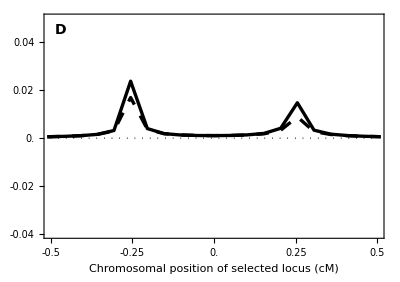

```mathematica
positionplotD=
Show[
 
 (*neo-W into XY*)
ListPlot[Table[{a, invasionplotXY[tryFAA, tryFAa, tryFaa, tryMAA, tryMAa, tryMaa, tryMA, tryMa, tryFA, tryFa, tryMdA, tryFdA, setr[x,a,m],setR[x,a,m],setχ[x,a,m]]}, {a, xplotmin - 0.01, xplotmax + 0.01, ((xplotmax + 0.01) - (xplotmin - 0.01))/npoints}],
  Joined -> True,
  PlotRange -> {yplotmin, All},
  PlotStyle -> Directive[Black, Thickness[lwd]],
  AxesOrigin -> {xplotmin, yplotmin},
  Frame -> {True, True, False, False}
  ],
 
 (*neo-Y into ZW*)
ListPlot[Table[{a, invasionplotZW[tryFAA, tryFAa, tryFaa, tryMAA, tryMAa, tryMaa, tryMA, tryMa, tryFA, tryFa, tryMdA, tryFdA,setr[x,a,m],setR[x,a,m],setχ[x,a,m]]}, {a, xplotmin - 0.01, xplotmax + 0.01, ((xplotmax + 0.01) - (xplotmin - 0.01))/npoints}],
  Joined -> True,
  PlotRange ->  {yplotmin, All},
  PlotStyle ->  Directive[Black, Thickness[lwd], Dashing[Medium]],
  AxesOrigin ->  {xplotmin, yplotmin},
  Frame ->  {True, True, False, False}
  ],
 
 Plot[0, {x, xplotmin, xplotmax}, PlotStyle -> {Black, Dotted}],
 
 PlotRange ->  {{xplotmin, xplotmax}, {yplotmin, yplotmax}},
 ImageSize ->  {xsize, xsize aspectratio },
 AspectRatio ->  aspectratio,
 PlotRangePadding ->  0,
 FrameTicks ->  {Table[{x, x, ticksize}, {x, xplotmin, xplotmax, xplotinterval}], Table[{y, y, ticksize}, {y, yplotmin, yplotmax, yplotinterval}]},
FrameTicksStyle->{{Directive[FontColor->White],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
 FrameStyle ->  {{Black, Thickness[lwd]}, {Black, Thickness[lwd]}, None, None},
 FrameLabel ->  {"Chromosomal position of selected locus (cM)", ""},
 BaseStyle ->  {FontFamily -> "Helvetica", FontSize -> 14},
 ImagePadding ->  Pad,
 Epilog ->  {
  Text[Style["D",14,Bold],Scaled@letpos],
  (* Rotate[Text[Style["Invasion fitness", 14], Scaled@ylabpos], 90 Degree]*)
   },
 PlotRangeClipping ->  False
 
 ]

Export[plotdir<>"PositionPlotD.pdf",%];
```

### Combination plot

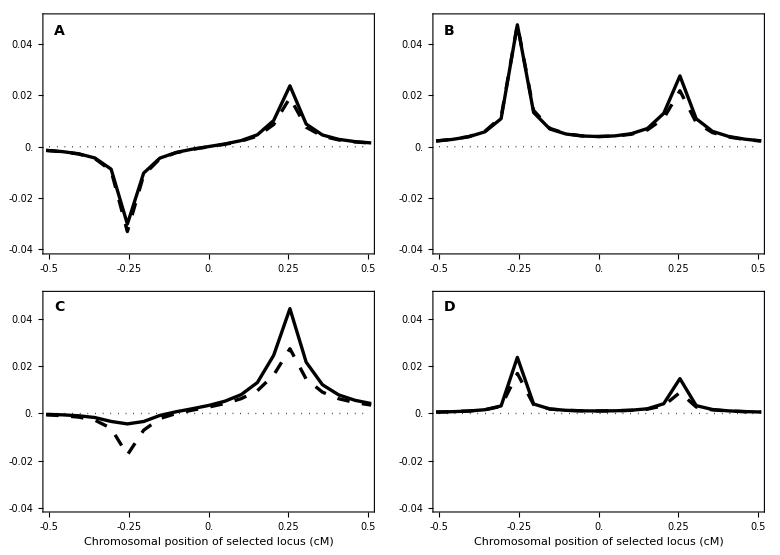

```mathematica
Legended[
GraphicsGrid[
{{positionplotA,positionplotB},{positionplotC,positionplotD}}
],
Placed[
LineLegend[
{
Directive[Thickness[0.1],Black],
Directive[Thickness[0.1],Black,Dashing[Medium]]
},
{
Style["neo-W in XY",16],
Style["neo-Y in ZW",16]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.5,0.5}
] 
]

Export[plotdir<>"PositionPlot.pdf",%];
```